## 作用量

我们在经典力学中就开始接触作用量了，从经典力学里面的三种表述方法，到量子力学的三种表述方法，作用量现身的频率可谓不低。

那么什么是作用量？

作用量是一个很特殊的量。要理解作用量是什么，需要从最小作用量原理出发，我们甚至应该把作用量定义成满足最小作用量原理的那个量，因为我们没有对作用量的严格定义，知识通过经验或者对称性等等来猜测作用量的，到底是不是真的有用的作用量，需要使用最小作用量原理来验证。

### 经典力学

经典力学有三种表述方法，分别是 Euler-Lagrange 方程，Hamiltonian 正则方程以及 Hamiltonian-Jacobi 理论。这三种理论中，Euler-Lagrange 方程和 Hamiltonian-Jacobi 理论都需要用到作用量。那么作用量在经典力学中，是什么意思呢？

#### Action Principal

作用量原理是拉氏形式中最核心的内容。在这里，作用量是拉氏量在时间上的积分，

S=(∫_ti)^tf L(q(t),q'(t),t)dt=S(q(t))

也就是说，拉氏量是时间t，广义坐标q(t)，广义坐标对时间的导数q’(t) 的函数。但是作用量却只是广义坐标q(t)的函数。

我们先不管作用量原理，先看看这个作用量到底是什么意思。在一个保守力系中，拉氏量可以写成动能减去势能

L=T-V

那么作用量就是

S=(∫_ti)^tf(T-V)dt

这个很有趣。当我们选定一条路径之后，例如我们选定一个经典路径之后，作用量就是动能和势能对时间的曲线之间的面积。这样说起来太抽象，我们可以看一个自由落体运动的例子（从 x=0 开始沿 x 轴负方向下落）：

L=1/2 m x'^2-m g x

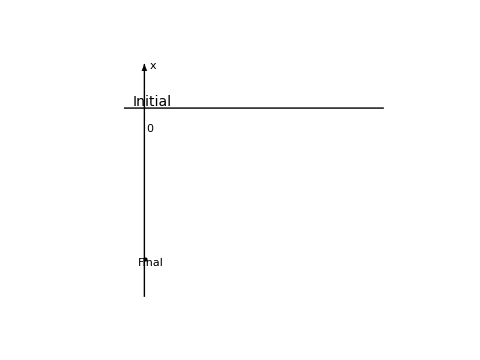

为了方便假定质量 m 为 1，那么如果我们选定经典轨道，那么就可以把动能和势能随着时间的变化关系画出来。

（经典轨道中，动能 T=(m g^2 t^2 )/2，势能 V=  - (m g^2 t^2) /2 ）

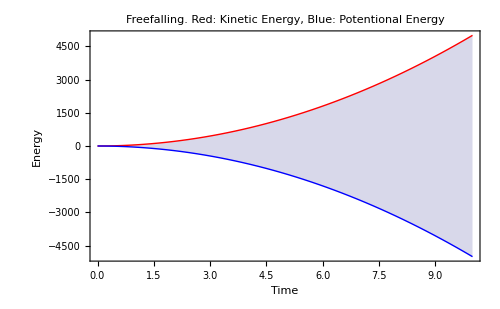

```mathematica
actEg1Plt1=Plot[{100 t^2/2,-100 t^2/2},{t,0,10},PlotLabel->"Freefalling. Red: Kinetic Energy, Blue: Potentional Energy",PlotStyle->{Red,Blue},FrameLabel->{"Time","Energy"},Filling->{1->{2}},Frame->True,ImageSize->500]
```

所以，对于这条经典路径，上面的阴影部分面积就是我们的路径积分的结果，即动能和势能的能量差值在整个时间上面的积分。

那么如果我们不是选取的经典路径呢？比如我们选取了这样一条路径：

x(t)=-g(t+1)^2

那么相应的，这条路径上的作用量就是对下面这个量在时间上的积分：

T-V = 2 g^2 (t+1)^2 - (- g^2 (t+1)^2)

不过在在这之前我们先写一个初步的用来绘制作用量的函数。

```mathematica
pltActionGr[q_,dq_,t1_,t2_,m_,g_]:=Plot[{1/2 m (dq)^2,m g q},{t,t1,t2},PlotLabel->"Red: Kinetic Energy, Blue: Potentional Energy",PlotStyle->{Red,Blue},FrameLabel->{"Time","Energy"},Filling->{1->{2}},Frame->True,ImageSize->500]
```

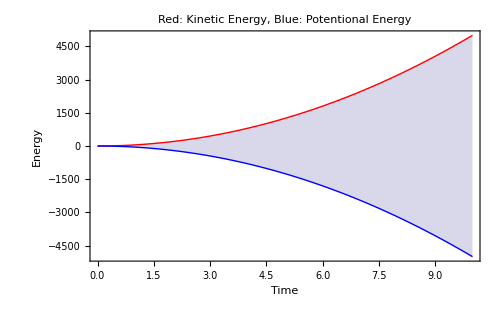

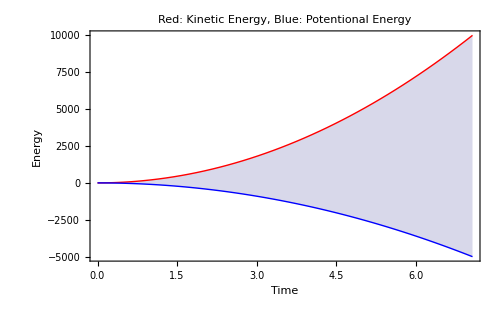

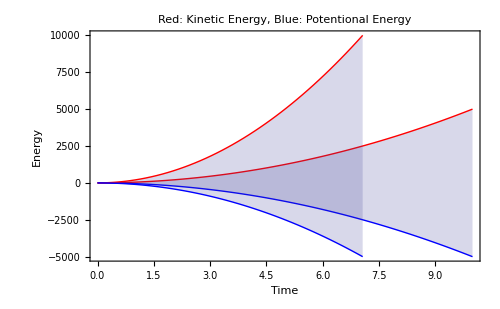

```mathematica
qEg1[t_]=-1/2 10 t^2;
actEg1Plt2=pltActionGr[qEg1[t],Evaluate[D[qEg1[t],t]],0,10,1,10]
qEg2[t_]=-10 t^2;
actEg1Plt3=pltActionGr[qEg2[t],Evaluate[D[qEg2[t],t]],0,Evaluate[√(-q/g)/.{q->qEg1[10],g->10}],1,10]
Show[actEg1Plt2,actEg1Plt3,PlotRange->{{0,10},{-5000,10000}}]
```

作用量就是阴影区域的面积。似乎看不出来。这种分析方法不理想。我们还是用数值算算吧。

```mathematica
qEg1[t_]=-1/2 10 t^2;
"The Action of Real Path is "<>
ToString[
NIntegrate[1/2 m (dq)^2-m g q/.{q->qEg1[t],dq->Evaluate[D[qEg1[t],t]],m->1,g->10},{t,0,10}]
]<>"."
qEg2[t_]=-10 t^2;
"The Action of New Path is "<>
ToString[
NIntegrate[1/2 m (dq)^2-m g q/.{q->qEg2[t],dq->Evaluate[D[qEg2[t],t]],m->1,g->10},{t,0,Evaluate[√(-q/g)/.{q->qEg1[10],g->10}]}]
]<>"."
```

The Action of Real Path is 33333.3.

The Action of New Path is 35355.3.

从面积数值来看，选定的新路径下面作用量变大了。
实际上大家可能注意到了，在作用量原理里面，我们所需要的基本假设少的可怜，我们连量纲、甚至能量守恒都不需要事先考虑（上面的例子中，新路径的能量不守恒，从图片里面上下部分不对称可以知道），只需要承认作用量原理，我们几乎获得所有的规则。这就是为什么作用量原理会显得更加基本。但是这也是很大的问题，从经典力学里面，我们似乎看不到为什么我们需要一个这样的原理，或者说，我们只知道这个原理起作用，但是并不是很明白为什么会有这个原理以及这个原理意味着什么。

从上面的保守力系的例子来看，最小作用量原理似乎要求整个过程中，动能和势能的相互转化要最小，否则会导致作用量变大。
为什么呢？
如果我们让能量转化的更多些，那意味着大的动能，或者说更高的速度，因此就意味着会用更少的时间来从起点到终点。

（原本是想尝试用例子来把问题看得更清晰，但是这里我并没有找到一个足够好的方法来展示这个原理的内涵。这部分说的好失败。我再试试量子的情况。）

### 关于力学体系

下面本来是要说一下量子里面的作用量的，但是在这之前，可以先来看看力学体系里面的不同的形式。先来一个表格。

经典 | 量子
最小作用量原理 | 路径积分
哈密顿正则方程 | 波动力学，矩阵力学
哈密顿-雅克比 | 路径积分

这里面最基本的应该是经典力学的作用量原理和 Euler-Langrange 方程，或者量子里面路径积分的形式。量子力学的路径积分形式比经典力学的作用量形式更近了一步。经典力学知识说，就是有这样一条路径是对的，粒子就要走这一条。但是这让人很奇怪，为什么要走这一条？当然，有个法国朋友说，物理不能问为什么，只能尝试去解释怎么工作。量子力学里面的路径积分的想法更近了一步。

### 量子

在量子世界中，似乎作用量的“意义“要更容易明白些。在路径积分理论中，位形空间中的传播子可以看做是（当然严格的要写成积分的样子，这里只做一个简单的意义上的呈现）

K=∑Constant e^(iS/ℏ)

传播函数是说，如果我们知道波函数的初态。那么可以通过传播函数来把波函数演化到下一步，与光学里面的惠更斯原理很像，虽然每条路都是等概率的，但是因为我们有个相因子S/ℏ，所以实际上，作用量的作用就是体现每条路径的比重/重要程度。所以上面的传播函数的形式来看，经典作用量S扮演了一个很核心的作用。

当然，在量子力学的传播函数的积分中，作用量S也连接了量子和经典这两个不同的研究范畴。因为经典作用量S很大时，几乎只有经典路径附近的路径才起作用，所以体系的性质也趋于经典。

## 草稿

/*不过我们不需要这么麻烦，在 Feymann Lectures 里面有一段讲这个的。我们模仿他。实际上我们可以把整个积分算出来。*/

我们可以再看看上抛运动的例子（初速度100[L]/[T]，实际路径：x=100t-1/2 g t^2, x’=100-g t；任选的路径：x=100t-1/2t, x’=100-t）：

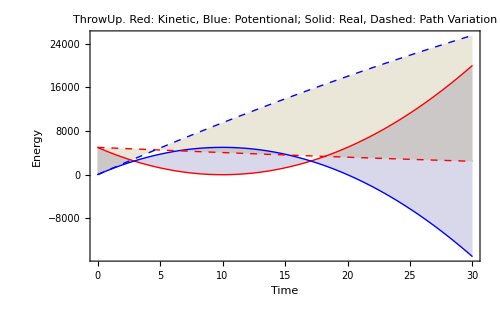

```mathematica
Plot[{1/2 (100-10t)^2,10(100t-5t^2),1/2 (100-t)^2,10(100t-1/2t^2)},{t,0,30},PlotLabel->"ThrowUp. Red: Kinetic, Blue: Potentional; Solid: Real, Dashed: Path Variation",PlotStyle->{Red,Blue,Directive[Red,Dashed],Directive[Blue,Dashed]},FrameLabel->{"Time","Energy"},Filling->{1->{2},3->{4}},Frame->True,ImageSize->500]
```